## Nested Sampling (Binominal)

```mathematica
(*Eine einzige Ziehung*)
n = 1000;
k = 502;
L[p_]:=Binomial[n,k]*p^k*(1-p)^(n-k);
lnL[p_]:=Log[Binomial[n,k]]+k Log[p]+(n-k)Log[1-p];

samplesize = 500;
livepoints = Table[RandomReal[{0.4,0.6}],samplesize];
deadpoints = {};
lnminLlist = {};
lnw = {};
Xi = {};
i = 1;
dlnZi =1;
```

```mathematica
While[dlnZi >10^-3,
(*Determine the position of the sample with the smallest Likelihood*)
lnLlist =Table[lnL[livepoints[[j]]],{j,1,samplesize}];
lnLmin = Min[lnLlist];
AppendTo[lnminLlist,lnLmin];
imin = Position[lnLlist,lnLmin][[1,1]];
AppendTo[deadpoints,livepoints[[imin]]];

(*Replace the sample with a new one with a bigger Likelihood*)
test=0;
While[test==0,
sample = RandomReal[{0.4,0.6}];
If[lnL[sample] > lnLmin ,livepoints[[imin]] =sample;test=1]];

(*Estimate the Prior Volume*)
AppendTo[Xi,Exp[(-i-√i)/samplesize]];
(*Evaluate the importance weight*)

If[i==1,lnwi =lnminLlist[[i]]-Log[2]+Log[(1-Xi[[i]])/2]];
If[i==2,lnwi =lnminLlist[[i]]+Log[1+Exp[lnminLlist[[i-1]]-lnminLlist[[i]]]]-Log[2]+Log[(1-Xi[[i]])/2]];
If[i>2,lnwi =lnminLlist[[i]]+Log[1+Exp[lnminLlist[[i-1]]-lnminLlist[[i]]]]-Log[2]+Log[(Xi[[i-2]]-Xi[[i]])/2]];
AppendTo[lnw,lnwi];

(*Evaluate Stopping Criterium*)

maxlnw = Max[lnw];
imax= Position[lnw,maxlnw][[1,1]];
If[i==1,lnZi=maxlnw];
If[i>1,lnZi =maxlnw +Log[1+∑_(j=1)^(Length[lnw]-1) Exp[Delete[lnw,imax][[j]]-maxlnw]]];

lndZi = Max[lnLlist]+(-i-√i)/samplesize;

dlnZi = lndZi + Log[1+Exp[lnZi-lndZi]]-lnZi;

If[Mod[i,1000]==0,Print[dlnZi]];
i += 1];
```

```mathematica
Print["Z Sampling: ",Exp[lnZi]," + ",Exp[lndZi]];
Print["Z analytisch: ",N[∫_0.4^0.6 L[p]ⅆp]];
```

```mathematica
Z =N[∫_0.4^0.6 L[p]ⅆp];
Plot[L[p]/Z,{p,0.4,0.6},PlotRange->All]

ListPlot[Table[{deadpoints[[j]],Exp[lnw[[j]]]/Exp[lnZi]},{j,1,Length[lnw]}]]
```

```mathematica
ListLinePlot[deadpoints]
```

```mathematica
∫_0.4^0.6 L[p]/Z pⅆp
mittelwert=Sum[Exp[lnw[[j]]]/Exp[lnZi]*deadpoints[[j]],{j,1,Length[lnw]}]
```

```mathematica
∫_0.4^0.6 L[p]/Z p^2 ⅆp-(∫_0.4^0.6 L[p]/Z pⅆp)^2
Sum[(deadpoints[[j]]-mittelwert)^2 Exp[lnw[[j]]]/Exp[lnZi],{j,1,Length[deadpoints]}]
```

```mathematica
(*K = 2'000*)
```

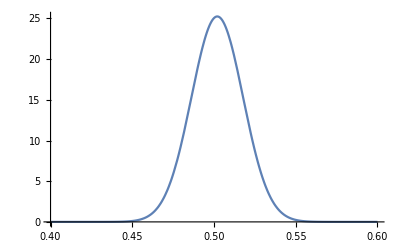

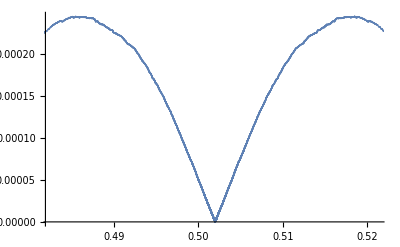

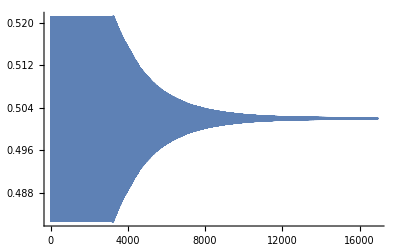

```mathematica
(*Mittelwert*)
0.5019960079692284
0.5021613806277577

(*Varianz*)
0.0002492482689613884
0.00024840890579087203
```